```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/feng/Library/CloudStorage/GoogleDrive-lyu00145@umn.edu/我的云端硬盘/mathematica/WWtt

```mathematica
pos=-0.05;
```

```mathematica
BarShell=ContourPlot[y==5000,{x,-0.06,0.06},{y,-3,7},LabelStyle->20,AspectRatio->0.4,ImageSize->650,FrameStyle->Directive[Black,Thickness[0.0015]],FrameLabel->{{None,None},{Style["δ_yt",Black],None}},AspectRatio->1, FrameTicks->{{None,Automatic},{Automatic,Automatic}},Epilog->{Inset[Style["LHC",Black,18],{pos,6}],Inset[Style["×10",ColorData[colorselecitonumber][17],15],{-0.015,6}],Inset[Style["0.16_-0.35^(+0.24)",Black,15],{-pos,6}],Inset[Style["HL-LHC",Black,18],{pos,5}],Inset[Style["±0.034",Black,15],{-pos,5}],Inset[Style["ILC-500",Black,18],{pos,4}],Inset[Style["±0.028",Black,15],{-pos,4}],Inset[Style["ILC-1000",Black,18],{pos,3}],Inset[Style["±0.01",Black,15],{-pos,3}],Inset[Style["CLIC-1400",Black,18],{pos,2}],Inset[Style["±0.038",Black,15],{-pos,2}],Inset[Style["FCC-ee",Black,18],{pos,1}],Inset[Style["±0.031",Black,15],{-pos,1}],
Inset[Style["FCC-hh",Black,18],{pos,0}],Inset[Style["±0.01",Black,15],{-pos,0}],
Inset[Style["MuC-3",Black,18],{pos,-1}],Inset[Style["×3",ColorData[colorselecitonumber][17],15],{-0.017,-1}],Inset[Style["0_-0.09^(+0.06)",Black,15],{-pos,-1}],
Inset[Style["MuC-10",Black,18],{pos,-2}],Inset[Style["0_-0.013^(+0.015)",Black,15],{-pos,-2}](*,
Inset[Style["MuC-3(VLQ)",Black,15],{pos,-1}],Inset[Style["-0.002",Black,15],{-pos,-1}],Inset[Style["MuC-10(VLQ)",Black,15],{pos,-2}],Inset[Style["-0.001",Black,15],{-pos,-2}]*)}](*,Placed[LegendBar,Scaled[{0.2,0.2}]]*);
```

```mathematica
BarColor=Join[Table[ColorData[colorselecitonumber][i],{i,5,10}],Table[ColorData[colorselecitonumber][i],{i,1,4}]]
```

{RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843]}

```mathematica
Table[ColorData[colorselecitonumber][i],{i,1,20}]
```

{RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]}

```mathematica
dat0=Transpose[{{Around[0.1*(1.16-1),{0.1*0.35,0.1*0.24}],Around[0,0.034],Around[0,0.028],Around[0,0.01],Around[0,0.038],Around[0,0.031],Around[0,0.01],Around[0,{0.06,0.09}/3],Around[0,{0.013,0.015}]},{6,5,4,3,2,1,0,-1,-2}}]
```

(0.0160.0350.024 | 6
0.0000.034 | 5
0.0000.028 | 4
0.0000.010 | 3
0.000.04 | 2
0.0000.031 | 1
0.0000.010 | 0
0.0000.0200.030 | -1
0.0000.0130.015 | -2)

```mathematica
dat1=Transpose[{{Around[0,{0.002,0}],Around[0,{0.001,0}]},{-1,-2}}]
```

{{00.00200.,-1},{00.00100.,-2}}

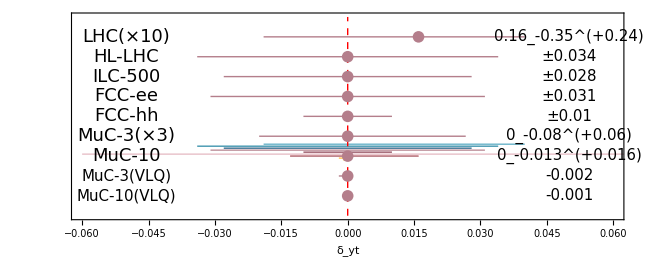

```mathematica
Show[BarShell,Graphics[{{BarColor[[1]],Rectangle[{0.1*(1.16-0.35-1),0.1*(6-0.3)},{0.1*(1.16+0.24-1),0.1*(6+0.3)}]}
,{BarColor⟦2⟧,Rectangle[{-0.034,0.1*(5-0.3)},{0.034,0.1*(5+0.3)}]},{BarColor⟦3⟧,Rectangle[{-0.028,0.1*(4-0.3)},{0.028,0.1*(4+0.3)}]},{BarColor⟦4⟧,Rectangle[{-0.031,0.1*(3-0.3)},{0.031,0.1*(3+0.3)}]},{BarColor⟦5⟧,Rectangle[{-0.01,0.1*(2-0.3)},{0.01,0.1*(2+0.3)}]},{BarColor⟦6⟧,Rectangle[{-0.06,0.1*(1-0.3)},{0.08,0.1*(1+0.3)}]},{BarColor⟦7⟧,Rectangle[{-0.013,0.1*(-0.3)},{0.016,0.1*(+0.3)}],{BarColor⟦8⟧,Rectangle[{-0.002,0.1*(-1-0.3)},{0.0,0.1*(-1+0.3)}]},{BarColor⟦9⟧,Rectangle[{-0.001,0.1*(-2-0.3)},{0.0,0.1*(-2+0.3)}]}},{Red,Dashed,Line[{{0,-3},{0,7}}]}}],ListPlot[dat0,PlotStyle->ColorData[colorselecitonumber][18]],ListPlot[dat1,PlotStyle->ColorData[colorselecitonumber][18],IntervalMarkersStyle->{"FenceWidth"->.5}]]
```

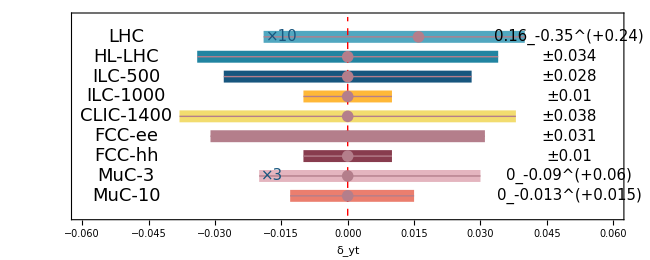

```mathematica
fign=Show[BarShell,Graphics[{{BarColor[[1]],Rectangle[{0.1*(1.16-0.35-1),6-0.3},{0.1*(1.16+0.24-1),6+0.3}]}
,{BarColor⟦2⟧,Rectangle[{-0.034,5-0.3},{0.034,5+0.3}]},{BarColor⟦3⟧,Rectangle[{-0.028,4-0.3},{0.028,4+0.3}]},{BarColor⟦8⟧,Rectangle[{-0.01,3-0.3},{0.01,3+0.3}]},{BarColor⟦9⟧,Rectangle[{-0.038,2-0.3},{0.038,2+0.3}]},{BarColor⟦4⟧,Rectangle[{-0.031,1-0.3},{0.031,1+0.3}]},{BarColor⟦5⟧,Rectangle[{-0.01,0-0.3},{0.01,0+0.3}]},{BarColor⟦6⟧,Rectangle[{-0.06/3,-1-0.3},{0.09/3,-1+0.3}]},{BarColor⟦7⟧,Rectangle[{-0.013,-2-0.3},{0.015,-2+0.3}]},{Red,Dashed,Line[{{0,-3},{0,7}}]}}],ListPlot[dat0,PlotStyle->ColorData[colorselecitonumber][18]](*,ListPlot[dat1,PlotStyle->ColorData[colorselecitonumber][18],IntervalMarkers->None]*)]
```

```mathematica
Export["dyt_all.pdf",fign,ImageResolution->200]
```

dyt_all.pdf

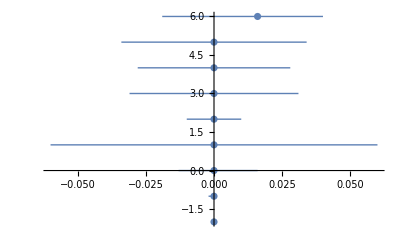

```mathematica
ListPlot[dat0]
```

```mathematica
ChartFCC=Graphics[{{White,EdgeForm[Directive[BarColor⟦1⟧,Thick]],Rectangle[{2.5-2-0.2,1.16-0.35},{2.5-1-0.2,1.16+0.24}]}
,{BarColor⟦2⟧,Rectangle[{2.5-1-0.04,1.16-0.35},{2.5-0.04,1.16+0.24}]}
,{BarColor⟦2⟧,Rectangle[{2.5+0.04,A16⟦1⟧},{2.5+0.04+1,A26⟦1⟧}]}
,{Darker[BarColor⟦2⟧],Rectangle[{2.5+0.04,A16FCC⟦1⟧},{2.5+0.04+1,A26FCC⟦1⟧}]}
,{White,EdgeForm[Directive[BarColor⟦3⟧,Thick]],Rectangle[{6.35-2-0.2,A12⟦2⟧},{6.35-1-0.2,A22⟦2⟧}]}
,{BarColor⟦3⟧,Rectangle[{6.35-1-0.04,A15⟦2⟧},{6.35-0.04,A25⟦2⟧}]}
,{BarColor⟦4⟧,Rectangle[{6.35+0.04,A16⟦2⟧},{6.35+1+0.04,A26⟦2⟧}]}
,{Darker[BarColor⟦4⟧],Rectangle[{6.35+0.04,A16FCC⟦2⟧},{6.35+1+0.04,A26FCC⟦2⟧}]}
,{BarColor⟦5⟧,Rectangle[{10.25-1-0.04,A15⟦4⟧},{10.25-0.04,A25⟦4⟧}]}
,{BarColor⟦6⟧,Rectangle[{10.25+0.04,A16⟦4⟧},{10.25+1+0.04,A26⟦4⟧}]}
,{Darker[BarColor⟦6⟧],Rectangle[{10.25+0.04,A16FCC⟦4⟧},{10.25+1+0.04,A26FCC⟦4⟧}]}
,{BarColor⟦7⟧,Rectangle[{14-1-0.04,A15⟦3⟧},{14-0.04,A25⟦3⟧}]}
,{BarColor⟦8⟧,Rectangle[{14+0.04,A16⟦3⟧},{14+1+0.04,A26⟦3⟧}]}
,{Darker[BarColor⟦8⟧],Rectangle[{14+0.04,A16FCC⟦3⟧},{14+1+0.04,A26FCC⟦3⟧}]}
,{BarColor⟦9⟧,Rectangle[{18-1-0.04,A15⟦5⟧},{18-0.04,A25⟦5⟧}]}
,{BarColor⟦10⟧,Rectangle[{18+0.04,A16⟦5⟧},{18+1+0.04,A26⟦5⟧}]}
,{Darker[BarColor⟦10⟧],Rectangle[{18+0.04,A16FCC⟦5⟧},{18+1+0.04,A26FCC⟦5⟧}]}
,{BarColor⟦12⟧,Rectangle[{21.75-0.5,A16⟦6⟧},{21.75+0.5,A26⟦6⟧}]}
,{Darker[BarColor⟦12⟧],Rectangle[{21.75-0.5,A16FCC⟦6⟧},{21.75+0.5,A26FCC⟦6⟧}]}
}];
```